## Definiciones

## Operadores

### Coin

```mathematica
-Graphics-;
```

```mathematica
n[α_,ϕ_]:={Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}
```

```mathematica
Paulis=PauliMatrix/@Range[3];
```

```mathematica
expCoin[θ_,α_,ϕ_]:=MatrixExp[(-ⅈ θ)/2(n[α,ϕ].Paulis)]
```

```mathematica
Coin[θ_,α_,ϕ_,t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoin[θ,α,ϕ]]]
```

```mathematica
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
Coin[θ,α,ϕ,t]
```

SparseArray[…]

### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

```mathematica
t=1;
Shift[t]
```

SparseArray[…]

### Unitaria

```mathematica
Unitary[θ_,α_,ϕ_,t_Integer]:=Shift[t].Coin[θ,α,ϕ,t]
```

```mathematica
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
Unitary[θ,α,ϕ,t]//Normal
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
Unitary[paramsCoin_List,t_Integer]:=Module[{coinProduct},
coinProduct=Dot@@(Coin[##,t]&@@@Reverse[paramsCoin]);
Shift[t].coinProduct]
```

```mathematica
θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;

Unitary[params,t]//Normal
Shift[t].Dot@@(Coin[##,t]&@@@Reverse[{{θ1,α1,ϕ1},{θ2,α2,ϕ2}}])//Normal
Shift[t].Coin[θ2,α2,ϕ2,t].Coin[θ1,α1,ϕ1,t]//Normal
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

## Funciones cálculos

### Estados de la moneda

```mathematica
state0={1.,0.};
state1={0.,1.};
plusX=1/Sqrt[2]{1.,1.};
minusX=1/Sqrt[2]{1.,-1.};
plusY=1/Sqrt[2.]{1,ⅈ};
minusY=1/Sqrt[2.]{1,-ⅈ};
```

```mathematica
HVecs=N[Normalize/@Eigenvectors[FourierMatrix[2]]];
HMinus=HVecs[[1]];
HPlus=HVecs[[2]];
```

### Hallar antípoda

```mathematica
FindAntipode[polar_,azimutal_]:=Module[{newPolar,newAzimutal},
{newPolar=π-polar,
newAzimutal=azimutal+π}
]
```

```mathematica
α=6π/10;
ϕ=0;
FindAntipode[α,ϕ]
```

{(2 π)/5,π}

### Estado final de la caminata después de t pasos

```mathematica
DQWL[coin0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[θ,α,ϕ,i]],{i,t}];
psi
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
DQWL[coin0,θ,α,ϕ,t]
```

{0,-0.672499+0.275336 ⅈ,0,0,-0.672499+0.140291 ⅈ,0}

```mathematica
DQWL[coin0_,paramsCoin_List,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[paramsCoin,i]],{i,t}];
psi
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};

θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;
DQWL[coin0,params,t]
```

{0,-0.672499+0.275336 ⅈ,0,0,-0.672499+0.140291 ⅈ,0}

### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
PosProbDistrib[DQWL[coin0,θ,α,ϕ,t],t]
```

{0.528064,0,0.471936}

### Distribución de probabilidad para cada uno de los pasos

```mathematica
PosProbDisTime[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@θ,N@α,N@ϕ,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
P1=PosProbDisTime[coin0,θ,α,ϕ,t]
```

{{0,1.,0},{0.528064,0,0.471936}}

```mathematica
PosProbDisTime[coin0_,paramsCoin_List,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@paramsCoin,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};

θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;
P2=PosProbDisTime[coin0,params,t]
```

{{0,1.,0},{0.528064,0,0.471936}}

### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[Chop[posProbDisTime.Range[-t,t]]]
```

```mathematica
t=1;
EV=ExpecValue[P2, t]
```

{0,-0.0561285}

### Determinar si la estrategia es ganadora o perdedora

```mathematica
WinningQ[expValsList_List] := 
  Which[
SameQ@@expValsList,"Indefinido",
    OrderedQ[expValsList], "Ganadora",
    OrderedQ[expValsList, GreaterEqual], "Perdedora",
    True, "No se puede determinar"
  ]
```

```mathematica
WinningQ[EV]
```

Perdedora

### Calcular posProbDistTime, expval y typeStrategy

```mathematica
CalculateData[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,θ,α,ϕ,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;

CalculateData[coin0,θ,α,ϕ,t]
```

{{{0,1.,0},{0.528064,0,0.471936}},{0,-0.0561285},Perdedora}

### Fijar θ y α, variar ϕ

```mathematica
ClearAll@VaryingPhi
```

```mathematica
VaryingPhi[coin0_,θ_,α_,nϕ_Integer,t_Integer]:=Module[{ϕ},
Table[
{ϕ=i *2π/nϕ,
CalculateData[coin0,θ,α,ϕ,t]}
,
{i,0,nϕ-1}
]
]
```

```mathematica
coin0=plusX;
θ=9π/5;
α=2 π/5;
nϕ=2;
t=1;
A=VaryingPhi[coin0,θ,α,nϕ,t]
```

{{0,{{{0,1.,0},{0.471936,0,0.528064}},{0,0.0561285},Ganadora}},{π,{{{0,1.,0},{0.528064,0,0.471936}},{0,-0.0561285},Perdedora}}}

### Fijar θ , variar α y ϕ

```mathematica
VaryingAlpha[coin0_,θ_,nα_Integer,nϕ_Integer,t_Integer]:=Module[{α},
Table[
{α=j*π/(nα-1),
VaryingPhi[coin0,θ,α,nϕ,t]}
,
{j,0,nα-1}
]
]
```

```mathematica
coin0=plusX;
θ=9π/5;
nα=2;
nϕ=2;
t=1;
B=VaryingAlpha[coin0,θ,nα,nϕ,t]
```

{{0,{{0,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}},{π,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}}}},{π,{{0,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}},{π,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}}}}}

### Variar θ, α y ϕ

```mathematica
ClearAll@VaryingTheta
```

```mathematica
VaryingTheta[psi0_,nθ_Integer,nα_Integer,nϕ_Integer,t_Integer]:=Module[{θ},
Table[
{θ=k*2π/nθ,
VaryingAlpha[psi0,θ,nα,nϕ,t]}
,
{k,0,nθ-1}
]
]
```

```mathematica
coin0=plusX;
nθ=2;
nα=2;
nϕ=2;
t=1;
F=VaryingTheta[coin0,nθ,nα,nϕ,t]
```

{{0,{{0,{{0,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}},{π,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}}}},{π,{{0,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}},{π,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}}}}}},{π,{{0,{{0,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}},{π,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}}}},{π,{{0,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}},{π,{{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}}}}}}}

### Extract data for FixedTimeExpValPlot

```mathematica
ExtractDataExpVal[fixedTimeExpValPlot_List]:=Module[{th,alph},
{th=F[[1,1]],
{alph,#[[1]]}->#[[2,2,-1]]&/@(
alph=#[[1]];
#[[2]]
)&/@F[[1,2]]}
]
```

```mathematica
ExtractDataExpVal[F]
```

{0,{{{0,0}→0,{0,π}→0},{{π,0}→0,{π,π}→0}}}

```mathematica
Module[{th,alph},
th=F[[1,1]];
{alph,#[[1]]}->#[[2,2,-1]]&/@(
alph=#[[1]];
#[[2]]
)&/@F[[1,2]]
]
```

{{{0,0}→0,{0,π}→0},{{π,0}→0,{π,π}→0}}

## Funciones gráficas

#### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

```mathematica
SphereColor=RGBColor["#DFF7FF"];
```

```mathematica
CH1=RGBColor["#9C0147"];
CH2=RGBColor["#DC0014"];
CH3=RGBColor["#FA742C"];
CH4=RGBColor["#FFB33C"];
CH5=RGBColor["#FFE04D"];
CC1=RGBColor["#80B83"];
CC2=RGBColor["#1E9B9D"];
CC3=RGBColor["#0472BD"];
CC4=RGBColor["#063DAC"];
CC5=RGBColor["#2C139B"];
```

#### Label coin

```mathematica
LabelCoinState[state0]:="0";
LabelCoinState[state1]:="1";
LabelCoinState[plusX]:="+_x"
LabelCoinState[minusX]:="-_x"
LabelCoinState[plusY]:="-_y"
LabelCoinState[minusY]:="-_y"
LabelCoinState[HMinus]:="H_-"
LabelCoinState[HPlus]:="H_+"
```

#### Probabilidad respecto al tiempo

```mathematica
PosProbDisTimePlot[posProbDisTime_List,opts:OptionsPattern[ArrayPlot]]:=
ArrayPlot[posProbDisTime,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0,
PlotLegends->BarLegend[
Automatic,
LegendLabel->""
]
]
```

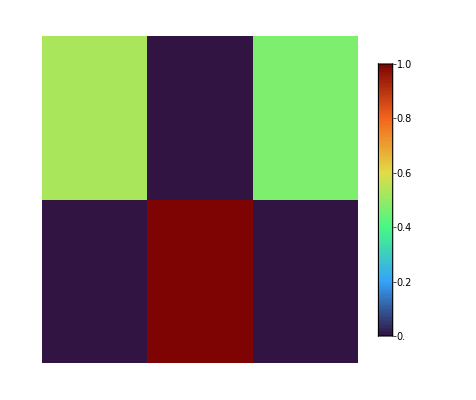

```mathematica
PosProbDisTimePlot[P2]
```

#### Valor de expectación respecto al tiempo

```mathematica
Clear@ExpValVsTimePlot
```

```mathematica
ExpValVsTimePlot[expecValue_List,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->All,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

```mathematica
ExpValVsTimePlot[{expecValues__List},opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->All,
Evaluate@opts
]
```

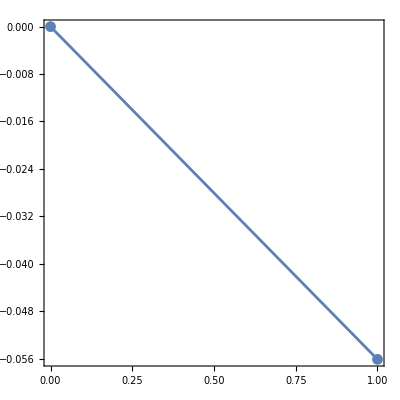

```mathematica
ExpValVsTimePlot[EV]
```

#### Valor de expectación para un tiempo fijo

```mathematica
FixedTimeExpValPlot[initCoinState_String,θ_,t_,results_List,nα_Integer,nϕ_Integer]:=Module[{data,alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer datos {α,φ,valor}*)
data=Flatten[Function[{a,sublist},{a,#[[1]],#[[5,t+1]]}&/@sublist]@@@results,1];

(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{2*i π/10,ToString[TraditionalForm[2*i π/nα]]},{i,0,nα}];
phiTicks=Table[{2*i*2π/nϕ,ToString[TraditionalForm[2*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{"Rainbow",{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",initCoinState,"     θ = ",θ,",     = ",t}]]]
```

#### Marcar el punto en la esfera de Bloch

```mathematica
PolarPoint[{r_,polar_,azimutal_}]:=Point[r*{Sin[polar] Cos[azimutal],Sin[polar] Sin[azimutal],Cos[polar]}]
```

```mathematica
ClearAll@SphereGraph
```

```mathematica
SphereGraph[initCoinState_String,θ_,results_List]:=Module[{points,sphere},
points=Join@@(Function[{a,sublist},{a,#[[1]],#[[2]]}&/@sublist]@@@results);
sphere=Graphics3D[{
Opacity[0.95],Glow[SphereColor],Black,Sphere[],
Opacity[1],PointSize[0.02],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,1.2}}],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{-1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,-1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,-1.2}}],

Text[Style["",14,Black],{1.3,0,0}],
Text[Style["",14,Black],{0,1.3,0}],
Text[Style["",14,Black],{0,0,1.3}],

Green,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[points,#[[3]]=="Ganadora"&]}],
Red,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[points,#[[3]]=="Perdedora"&]}],
Black,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[points,#[[3]]=="Indeterminado"&]}],
Gray,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[points,#[[3]]=="No se puede determinar"&]}]
},
Boxed->False,
PlotLabel->Row[{"c_0 = ",initCoinState,",    θ = ",θ}]
]
]
```